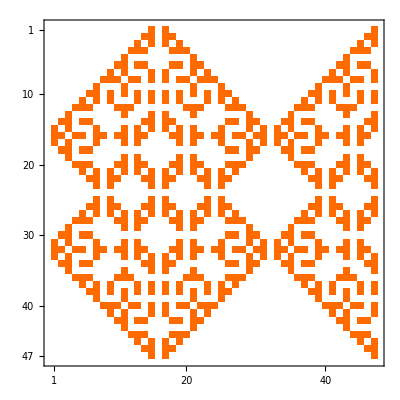
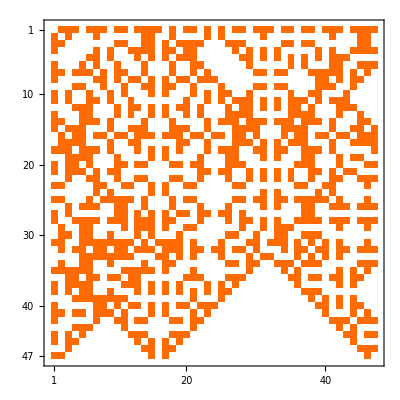
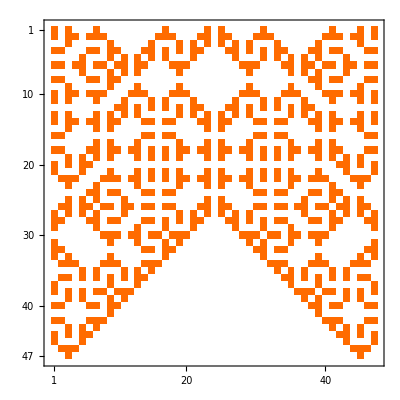
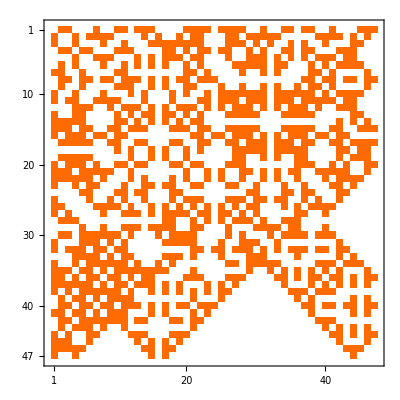
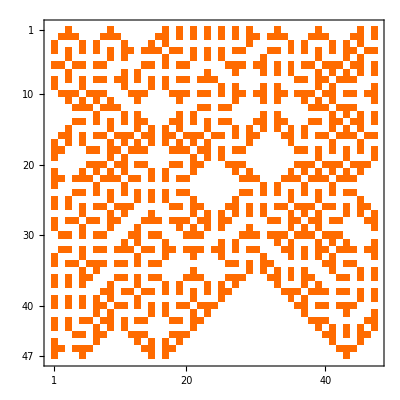
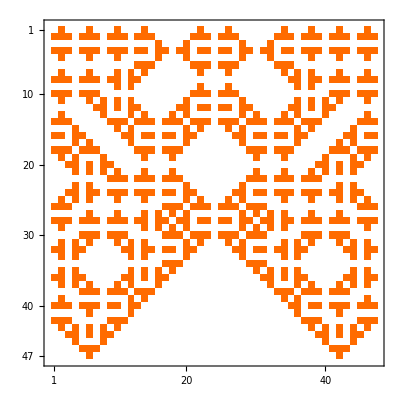
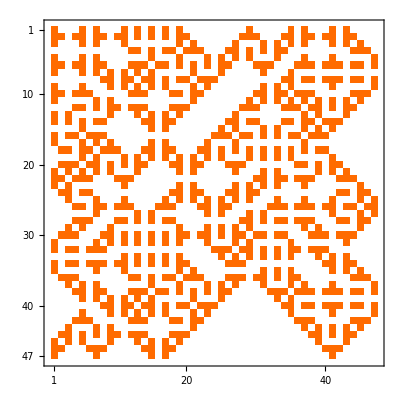
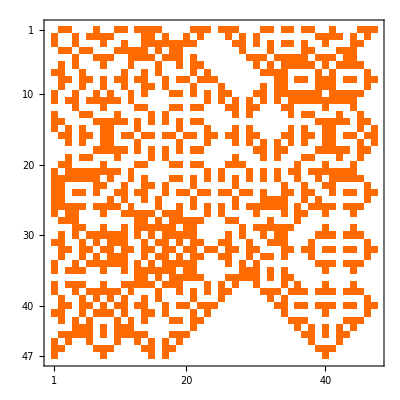

```mathematica
n=47;
Nu=NullSpace[AdjacencyMatrix[GridGraph[{n,n}]]+IdentityMatrix[n*n],Modulus->2];
d=Dimensions[Nu][[1]];
Table[MatrixPlot[ArrayReshape[Nu[[b,1;;n*n]],{n,n}]],{b,1,d}]
```